## Newton — Problem Set 1 — Solution

### 1. Can Speed be Proportional to Distance, rather than Time?

First, let’s quote from Sagredo’s proposal and Salviati’s counter-argument on pp. 167-168. Sagredo: “The speed acquired by a body in falling four cubits would be double the speed acquired in two cubits and this latter speed would be double that acquired in the first cubit.” Salviati: “If the velocities are in proportion to the spaces traversed, or to be traversed, then these spaces are traversed in equal intervals of time; if therefore, the velocity with which the falling body traverses a space of eight feet were double that with which it covered the first four feet (just as the one distance is double the other), then the time intervals required for these passages would be equal. But for one and the same body to fall eight feet and four feet in the same time is possible only in the case of instantaneous motion [discontinuous motion, which is of course impossible].”

Second, so that we have the possible modern counterexample to Salviati’s reasoning at hand, let’s re-plot the function. In the plot below, the function exactly the same, but the focus of the plot is now on 0<t<0.4 and 0<x<0.35:

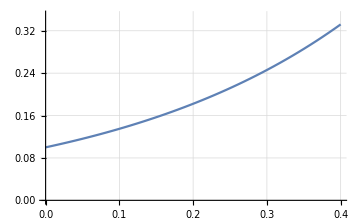

```mathematica
Plot[x0 Exp[α t]/.{x0-> 0.1, α->3} , {t, 0, 0.4}, PlotRange->{{0.0,0.4},{0.0,0.35}}, GridLines->Automatic]
```

This function simply will not do. It is not a counterexample. Two objections are apparent (the first unfixable, and the second fixable, but does not remedy the first): (1) At t=0, which was meant to be the time that the motion started, the velocity is already non-zero, as one can see from the slope of the above graph of x vs. t. On pp. 163-164, Salviati has already argued that this is impossible. When a body is dropped, it does not immediately pick up a non-zero velocity. The fact that an exponential always has a tiny initial velocity, is damning and unfixable as far as I can tell. (2) At t=0, the position is already non-zero. This is fixable. We just subtract x_0 from the solution, and we get this plot:

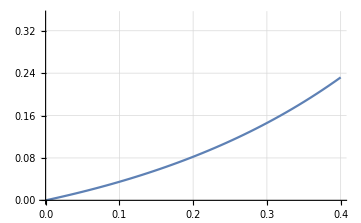

```mathematica
Plot[x0 (Exp[α t]-1)/.{x0-> 0.1, α->3} , {t, 0, 0.4}, PlotRange->{{0.0,0.4},{0.0,0.35}}, GridLines->Automatic]
```

However, this is no longer a solution of the equation  v = αx. Instead, we now have a solution of the equation  v = α(x+β), now with x(0)=0, as we desire, and a new constant β that is the x(0) from our prior solution. It still suffers from the first damning objection (the velocity at t=0 is already non-zero). Furthermore, I don’t think Sagredo intended for his proposal to allow for a constant β when he said on p. 167: “Uniformly accelerated motion is such that its speed increases in proportion to the space traversed.”

To conclude, Salviati’s counter-argument is simple and powerful and comes to the same conclusion as we have come to with all the power of calculus and differential equations in our hands, namely, that there is no good solution to the problem of uniformly accelerated motion, if by “uniformly accelerated” we use Sagredo’s proposal.

### 2. The Difference Between Rolling and Falling

(a) One would expect a ball to have more speed if it slides without friction because all of the gravitational potential energy has been converted to translational kinetic energy. NB: if it rolls due to friction it is not that energy is lost to friction, because we are thinking here of either perfect rolling (no slippage), or perfect sliding (no rotation), neither of which results in the loss of potential energy to heat. If it rolls due to friction, some of the kinetic energy is now in rotational kinetic energy, and there must be a corresponding amount less of translational kinetic energy.

(b) In the language around Fig. 45, Galileo has been very detailed, and I think the reason is that in his experiments, he is carefully trying to avoid rotational motion. He wants the plane to be “hard and smooth” and the ball to be “perfectly round, so that neither plane nor moving body is rough.”

His hanging-by-a-nail experiment (see Fig. 46) is another example wherein he is avoiding as much as possible contaminating the experiment with rotational motion and rotational kinetic energy.

As a third point in the text where it is becoming clear that Galileo is doing his very best to avoid rotational motion and rotational kinetic energy, we have his description at the bottom of p. 178: His wooden molding was “very straight, smooth, and polished, and having lined it with parchment, also as smooth and polished as possible, we rolled along it a hard, smooth, and very round bronze ball.” I can visualize what Galileo has set up, I can imagine the bronze ball sliding rather than rolling, at least if the plane were steep, and I even wonder if “rolling” is a translation error.

In fact, it must be a translation error, because a rolling ball has 2/7 of its energy in rotational kinetic energy (this is a complicated calculation, but trust me), so only 5/7 of the gravitational potential energy is in translational kinetic energy, and surely Galileo would have noticed a reduction in speed in the amount of √(5/7) (which is a 15.5% reduction) for the rolling ball.

### 3. 1, 3, 5, ... Sagredo is the king of straightforward arguments

(a) BFG and FPQ are the same size and shape as ABC:









(b) After cutting up rectangles N?CI into two triangles and QFIO into four triangles, we have:



So Row 1 has 1 triangle: ABC.

Row 2 has 3 triangles:  BFG, BCG, and CGI.

Row 3 has 5 triangles: FPQ, GFQ, GQT, IGT, and ITO. To identify these, I had to add the letters S, T, and U to the diagram.

It is entirely clear that we will get another two triangles in each successive row.

### 4. Galilean Relativity

(a) The thrower is moving eastward at 2 π 3960 / 24=1036.73 miles per hour. The air molecules a mile above the thrower are moving eastward at 2π 3961/24=1036.98 miles per hour. The ball does not pick up eastward velocity as it goes higher, so when it reaches its apex, the air molecules are moving eastward past it at 0.25 miles per hour.

(b) Since the molecules in the air a mile above us remain directly above us, and the ball is falling behind those air molecules in their movement eastward, it must be that the ball falls behind. In other words, it will land to the west of us.

(c) Ignoring air resistance, the required speed would be:

 v=√(2gh)=√(2·80000 miles/hour^2·1mile)=√(160000 miles^2/hour^2)=400 miles/hour
 
The ball would be in the air a total time of 800/80,000 hours = 0.01 hours = 36 seconds. In 0.01 hours, falling at most at a rate of 0.25 miles/hour behind (that’s at the apex, it would be less on the way up and down), that would be less than 0.0025 miles or 13.2 feet. It’s not zero, but good luck setting up that experiment accurately enough to see the effect.

The bottom line is that it is in principle detectable that we are on a rotating rather than translating slab of earth, but in practice it is not. In other words, Galilean relativity, which argues that translational motion is in principle experimentally undetectable, in practice applies to the Earth’s rotating motion too.